# Self-encoding 𝒜

Dieses Worksheet für das “finale” Ergebnis der Einsteinkorrigierten Funktion 𝒜 basiert auf dem Holographic 𝒜-Worksheet der Thesis und auf “Symmetrie für Bardeen.nb” aus Calc12.

An dem self-encoding-Modell (h_α) sind seit Calc12 (Mai 2014) keine Rechnungen mehr vorgenommen worden, nicht zuletzt weil bereits das holografische Modell erhebliche Schwierigkeiten aufwies und zu keinem hübschen Ergebniss führte.

## 0. Definitionen

Wir verwenden hier eine von der üblichen Notation abweichende Definition:
L’ = L/(2^(1/α)) sodass die Poler wie gewohnt 1+z^Potenz=0 sind, also auf dem Einheitskreis liegen. Damit ist z=r/L’.

```mathematica
Table[Log[2+n],{n,0,4}] // N
```

{0.693147,1.09861,1.38629,1.60944,1.79176}

```mathematica
halpha[z_,n_] = z^(3+n)/(z^α+1)^((3+n)/α)
α0[n_] := (3+n)/Log[2+n] * Log[(3+n)/2];
(* das grosse V aus der Thesis, der 3+n Integration Kernel *)
bigV[z_,n_] = 1/z^(2+n) D[halpha[z,n],z]//Together
(* das kleine v aus der Thesis: 1d integration Kernel *)
vSide[z_,n_, sign_:1] = z^(1+n) If[sign<0, (-1)^n bigV[-z,n], bigV[z,n]]
vEff[z_,n_] = vSide[z,n,+1]HeavisideTheta@Re@z + vSide[z,n,-1]HeavisideTheta@Re[-z]
vEff[z_,n_,α_] = vEff[z,n]/.α-> α;
```

z^(3+n) (1+z^α)^(-(3+n)/α)

(3+n) (1+z^α)^(-1-3/α-n/α)

z^(1+n) If[sign<0,(-1)^n bigV[-z,n],bigV[z,n]]

(-1)^n (3+n) (1+(-z)^α)^(-1-3/α-n/α) z^(1+n) HeavisideTheta[-Re[z]]+(3+n) z^(1+n) (1+z^α)^(-1-3/α-n/α) HeavisideTheta[Re[z]]

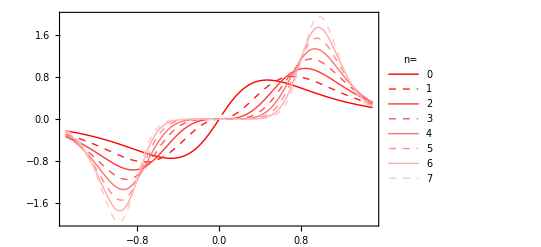

```mathematica
Plot[Table[vEff[z,n, α0[n]],{n,0,7}] //Evaluate, {z,-1.5,1.5},
PlotStyle-> MapIndexed[{If[EvenQ@First@#2, Dashed,{}],Blend[{Red,White},#1]}&, Rescale@Range@10],
(*PlotStyle->(Riffle[#,{Dashed,#}&/@Reverse[#]]& [ColorData[9,"ColorList"]]),*)
PlotLegends-> LineLegend[Table[n,{n,0,7}],LegendLabel-> "n="],
PlotRangePadding->None,
Frame-> True
]
```

## 1. Polstellen extrahieren

Code hier komplett aus holo-A-thesis.nb geholt.

```mathematica
(* Automatische Nullstellenbestimmung klappt nicht gut, zuviele Unsicherheiten ueber den Wert von α und so. Daher hier manuell konstruiert. *)
```

```mathematica
polstellen[α_] = Table[ Exp[I Pi (1+ 2k)/α],{k,0,Stehe auf dem Schlauch}]
```

Table::iterb: Iterator {k, 0, auf\ dem\ Schlauch\ Stehe} does not have appropriate bounds.

Table[Exp[(ⅈ π (1+2 k))/α],{k,0,auf dem Schlauch Stehe}]

```mathematica
Residue[3 (1+(-z)^α)^(-1-3/α) z /. α-> 2,{z,Exp[I Pi (1+2 2)/α]/.α-> 2}]
```

Residue[(3 z)/((1+z^2)^(5/2)),{z,ⅈ}]